# SimulationFunctions

## Tyson Jones tyson.jones@monash.edu August 2017

## WavefunctionSolver Package Test

```mathematica
Clear["Global`*"]
```

## Import

The location of the folder containing the package must be added to the paclet directories

In rare circumstances, the PacletManager` context will not be known, and must be prepended to the below call

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< WavefunctionSolver`
```

The available functions and their options:

```mathematica
?WavefunctionSolver`*
```

```mathematica
(* HAVE OPTION InitNormalize -> True (to normalise the wavefunction before evolution) *)
```

```mathematica
PlotEvolution[
	Exp[-space^2-time space ],
	{space, -5, 5},
	{time, 0, 3},
	Potential -> space^2,
	PlotRange -> {0, 10},
	AxesLabel -> {"a", "b"},

	PotentialPlotOptions -> {PlotStyle -> {Blue}},
	LegendLabel -> "hi",
	LegendFunction -> Framed,
	AnimationRate -> 4
	
]
```

## One/Two Space Dimensions

```mathematica
testheldplot = Hold[ 
	PlotWavefunction[
			(#1 + #2&)[x, t],
			{x, -5, 5},
			
			(* kill the sources of slow animation (we'll restore externally *)
			Potential -> None,
		    ShowColorBar -> False
		]
]
```

Hold[PlotWavefunction[(#1+#2&)[x,t],{x,-5,5},Potential→None,ShowColorBar→False]]

```mathematica
Animate[
	ReleaseHold @
	Hold[
	Show[
		ReleaseHold[%], 
		Plot[x, {x, -5, 5}]
	]
	],
	{t, 0, 3}
]
```

```mathematica
Head[%]
```

Hold

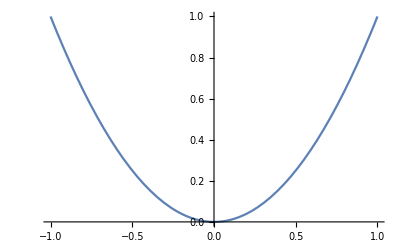

```mathematica
testp = Plot[x^2, {x, -1, 1}, PlotRange-> {0, 1}]
```

```mathematica
PlotRange[testp]
```

{{-1.,1.},{0.,1.}}

```mathematica
PlotRange[testp] = {{-
```

```mathematica
sometestfunc
```

Exp[-#1^2-#1 #2]&

```mathematica
(* SLOW *)

Animate[
	
		PlotWavefunction[
			sometestfunc[x, t],
			{x, -5, 5},
			
			(* kill the sources of slow animation (we'll restore externally *)
			Potential ->(#^2&),
		    ShowColorBar -> False
		],
		{{t, 0, "time"}, 0, 5}
]

(* SLOW *)

Animate[
	Show[
  
		PlotWavefunction[
			sometestfunc[x, t],
			{x, -5, 5},
			
			(* kill the sources of slow animation (we'll restore externally *)
			Potential -> None,
		    ShowColorBar -> False
		],
		WavefunctionSolver`PlotFunctions`PackagePrivate`plot1DPotential[
		#^2&, {-5, 5}, Automatic
		]

	],
	{{t, 0, "time"}, 0, 5}
]

(* FAST *)

testpotentialplot = WavefunctionSolver`PlotFunctions`PackagePrivate`plot1DPotential[
		#^2&, {-5, 5}, Automatic
		];
Animate[
	Show[
  
		PlotWavefunction[
			sometestfunc[x, t],
			{x, -5, 5},
			
			(* kill the sources of slow animation (we'll restore externally *)
			Potential -> None,
		    ShowColorBar -> False
		],
		testpotentialplot

	],
	{{t, 0, "time"}, 0, 5}
]
```

```mathematica
PlotEvolution[
	Exp[-space^2-time space ],
	{space, -5, 5},
	{time, 0, 3},
	Potential -> space^2,
	PlotRange -> {0, 10}
]
```

WavefunctionSolver`SimulationFunctions`PackagePrivate`animate1DEvolution[WavefunctionSolver`SimulationFunctions`PackagePrivate`combine1DProbPotentialPlots[Hold[PlotWavefunction[Function[{space,time},ⅇ^(-space^2-space time)][space,time],{space,-5,5},Potential→None,ShowColorBar→False,Evaluate[WavefunctionSolver`SimulationFunctions`PackagePrivate`extractOptions[Potential→space^2,PlotRange→{0,10},WavefunctionSolver`SimulationFunctions`PackagePrivate`plotOptionFunctions1D]]]],WavefunctionSolver`PlotFunctions`PackagePrivate`plot1DPotential[Function[space,space^2],{space,-5,5},Automatic,Potential→space^2,PlotRange→{0,10}]],{time,0,3}]

```mathematica
sometestfunc = Exp[-#1^2-#1 #2] &;

	Animate[
	PlotWavefunction[
		sometestfunc[x, t],
		{x, -5, 5},
		PlotRange -> {0, 10},
		ShowColorBar -> False
	],
	{t, 0,3}
	]

	PlotRange[%]
```

PlotRange::gtype: Manipulate is not a type of graphics.

PlotRange[]

```mathematica
(* PASS POTENTIAL AS AN OPTION (for both explicit and to be found) *)
(* not plotting Potential can be achieved by PotentialTransform -> 0 *)
(* have potential passed explicitly, but default it to 1 or something. Never use Potential option numerically *)
```

```mathematica
Clear[PlotEvolution]
```

```mathematica
(* 
	1D
*)

(* explicit time dependence *)

PlotEvolution[
	dynamicWavef_,
	{x_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	{t_Symbol, _?NumericQ, _?NumericQ}  (* time *)
] :=
	"1D space: " <> ToString[x] <> ", time: " <> ToString[t]
	
PlotEvolution[
	dynamicWavef_,
	dom:{_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	{t_Symbol, dur:_?NumericQ}              (* time *)
] :=
	PlotEvolution[dynamicWavef, dom, {t, 0, dur}]

(* find evolution *)

PlotEvolution[
	dynamicWavef_,
	potential_, 
	{x_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	duration_?NumericQ                  (* time *)
] :=
	"1D space: " <> ToString[x] <> ", duration: " <> ToString[duration]
	
(* 
	2D
*)	

(* explicit time dependence *)

PlotEvolution[
	dynamicWavef_,
	{x_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	{y_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	{t_Symbol, _?NumericQ, _?NumericQ}  (* time *)
] :=
	"1D space: " <> ToString[x] <> ", 2D space: " <> ToString[y] <> ", time: " <> ToString[t]

PlotEvolution[
	dynamicWavef_,
	dom1:{x_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	dom2:{y_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	{t_Symbol, dur:_?NumericQ}  (* time *)
] :=
	PlotEvolution[dynamicWavef, dom1, dom2, {t, 0, dur}]
	
(* find evolution *)

PlotEvolution[
	dynamicWavef_,
	potential_, 
	{x_Symbol, _?NumericQ, _?NumericQ}, (* space *)
	{y_Symbol, _?NumericQ, _?NumericQ},
	duration_?NumericQ                  (* time *)
] :=
	"1D space: " <> ToString[x] <> ", 2D space: " <> ToString[y] <> ", duration: " <> ToString[duration]
```

## solving evolution

```mathematica
FindEvolution[
	Exp[-x^2 - y^2],
	{x, -5, 5},
	{y, -6, 6},
	10
]
```

FindEvolution[ⅇ^(-x^2-y^2),{x,-5,5},{y,-6,6},10]

## passing evolution

### symbolic

```mathematica
PlotEvolution[
	Exp[-space^2-time],
	{space, -5, 5},
	{time, 0, 10}
]
```

```mathematica
PlotEvolution[
	Exp[-x^2 - y^2-t],
	{x, -5, 5},
	{y, -6, 6},
	{t, 0, 10}
]
```

1D space: x, 2D space: y, time: t

```mathematica
PlotEvolution[
	Exp[-x^2 -t],
	{x, -5, 5},
	{t, 10}
]
```

1D space: x, time: t

```mathematica
PlotEvolution[
	Exp[-x^2 - y^2-t],
	{x, -5, 5},
	{y, -6, 6},
	{t, 10}
]
```

1D space: x, 2D space: y, time: t

## finding evolution

```mathematica
PlotEvolution[
	Exp[-x^2],
	x^2,
	{x, -5, 5},
	10
]
```

1D space: x, duration: 10

```mathematica
PlotEvolution[
	Exp[-x^2 - y^2],
	x^2+ y^2,
	{x, -5, 5},
	{y, -5, 5},
	10
]
```

1D space: x, 2D space: y, duration: 10

## solving general pde